## Fitting sigma dan eden

### Memisahkan data Pr vs ED dlm 1 file tersendiri

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP0.E+00.dat"}],{Number,Number,Number,Number,Number,Number}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup0E0.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\efpc_gup0E0.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\efpc_gup1E-7.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-08.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-8.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\efpc_gup1E-8.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-09.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-9.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\efpc_gup1E-9.dat

### Memisahkan data σ (= Pr-Pt) vs ED dlm 1 file tersendiri

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP0.E+00.dat"}],{Number,Number,Number,Number,Number,Number}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup0E0.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\sfpc_gup0E0.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\sfpc_gup1E-7.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-08.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-8.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\sfpc_gup1E-8.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-09.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-9.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\sfpc_gup1E-9.dat

### fitting anisotropik

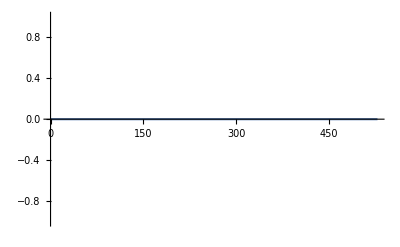

0.

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup0E0.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]}(*,Epilog->{PointSize[0.02],Map[Point,data]}*),PlotRange->Full]
```

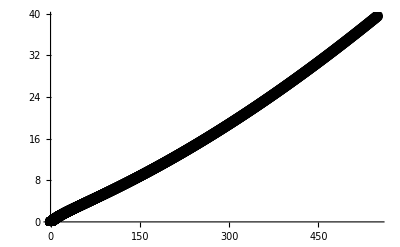

0.03276270690402464 + 0.0732724184678019*P0 - 0.0002845138865487051*P0**2 + 1.899265482204056e-6*P0**3 - 5.542478357273446e-9*P0**4 + 
     -  7.919729184670085e-12*P0**5 - 4.411910834615863e-15*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-7.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

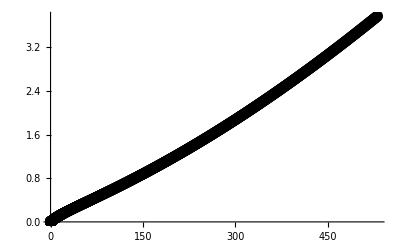

0.007047263002061006 + 0.007357568004071337*P0 - 0.000030457363087701862*P0**2 + 2.089265764280977e-7*P0**3 - 6.321235153591108e-10*P0**4 + 
     -  9.365561598013083e-13*P0**5 - 5.407853093925535e-16*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-8.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

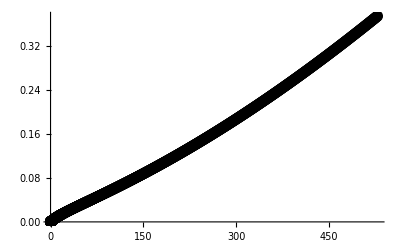

0.0007421020716274209 + 0.0007360498485325009*P0 - 3.066382135041724e-6*P0**2 + 2.1094050479548345e-8*P0**3 - 6.405883199257561e-11*P0**4 + 
     -  9.526370137661879e-14*P0**5 - 5.5210560366107184e-17*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-9.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

### fitting energy density GUP 0E0

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 0E0 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup0E0.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]],dataOuterCore[[2]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

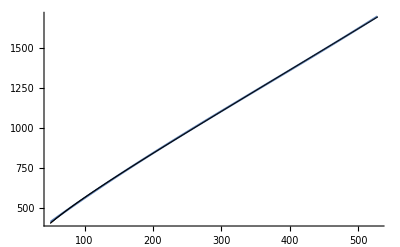

254.572+3.27227 P0-0.00199025 P0^2+1.84396×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP0E0=fitted
```

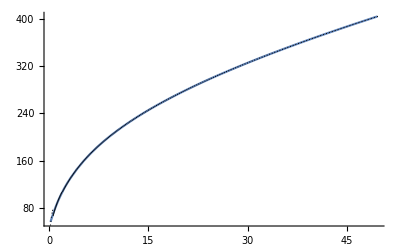

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16,P0^17},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP0E0=fitted;
```

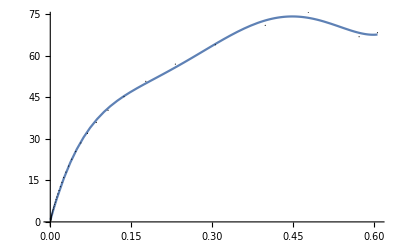

0.426006+714.24 P0-4571.21 P0^2+16153.3 P0^3-26410.3 P0^4+15662.1 P0^5

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4,P0^5},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP0E0=fitted
```

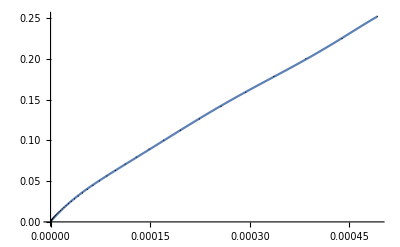

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP0E0=fitted
```

#### Cek hasilnya

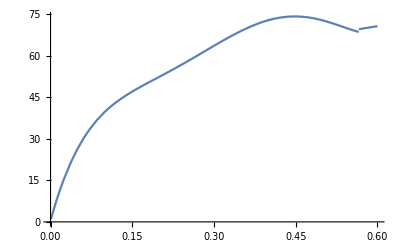

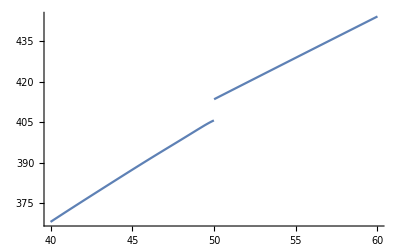

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP0E0;
FED2[P0_]=fitOuterCoreGUP0E0;
FED3[P0_]=fitInnerCrustGUP0E0;
FED4[P0_]=fitOuterCrustGUP0E0;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP0E0//FortranForm
```

254.57247440600335 + 3.2722668135019912*P0 - 
     -  0.0019902480708849125*P0**2 + 1.843962716723806e-6*P0**3

```mathematica
fitOuterCoreGUP0E0//FortranForm
```

49.26785125407585 + 39.11737020657924*P0 - 
     -  6.016128303060254*P0**2 + 0.3414923990896232*P0**3 + 
     -  0.18952907983055753*P0**4 - 0.06660361609394749*P0**5 + 
     -  0.01151087018516792*P0**6 - 0.0012890911262028622*P0**7 + 
     -  0.00010152320471437593*P0**8 - 
     -  5.8358103065480955e-6*P0**9 + 
     -  2.493373166744397e-7*P0**10 - 
     -  7.968694825132823e-9*P0**11 + 
     -  1.898165892923205e-10*P0**12 - 
     -  3.3213117284620262e-12*P0**13 + 
     -  4.144329953328089e-14*P0**14 - 
     -  3.490034358766075e-16*P0**15 + 
     -  1.7773505419267266e-18*P0**16 - 
     -  4.133909658617962e-21*P0**17

```mathematica
fitInnerCrustGUP0E0//FortranForm
```

0.42600647956391097 + 714.239562187894*P0 - 
     -  4571.210848278951*P0**2 + 16153.31540875086*P0**3 - 
     -  26410.273422295468*P0**4 + 15662.08708827156*P0**5

```mathematica
fitOuterCrustGUP0E0//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 
     -  6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 
     -  1.299108445236239e14*P0**4 + 2.097713931761943e17*P0**5 - 
     -  1.297185952864878e20*P0**6

### fitting energy density GUP 1Em7

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em7 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-7.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={(*dataOuterCore[[1]],dataOuterCore[[2]]*)};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

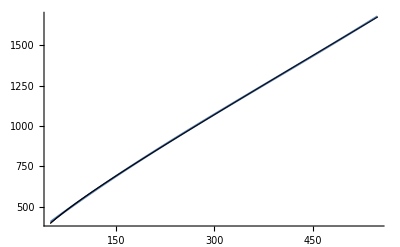

251.073+3.18009 P0-0.002004 P0^2+1.72437×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em7=fitted
```

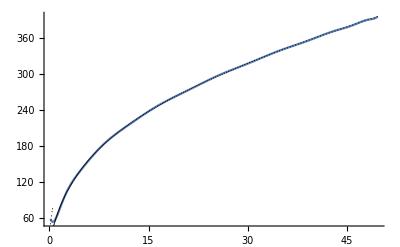

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em7=fitted;
```

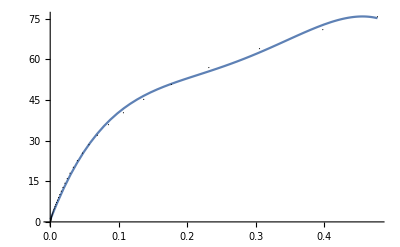

0.659656+658.782 P0-3385.41 P0^2+8513.26 P0^3-7598.18 P0^4

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em7=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em7=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

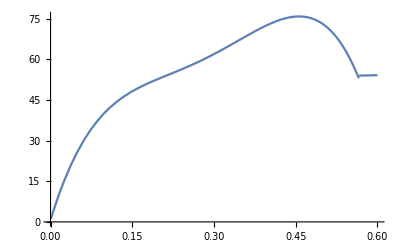

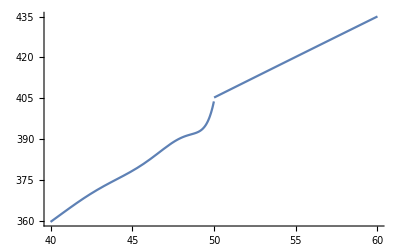

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em7;
FED2[P0_]=fitOuterCoreGUP1Em7;
FED3[P0_]=fitInnerCrustGUP1Em7;
FED4[P0_]=fitOuterCrustGUP1Em7;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em7//FortranForm
```

251.0731948102463 + 3.1800886693528474*P0 - 0.0020040035670855975*P0**2 + 1.7243713851215077e-6*P0**3

```mathematica
fitOuterCoreGUP1Em7//FortranForm
```

67.35232299097427 - 59.58608956261303*P0 + 82.73071434070408*P0**2 - 39.401804870651645*P0**3 + 10.799526030864467*P0**4 - 
     -  1.9127094225450478*P0**5 + 0.2325906052895863*P0**6 - 0.02016303442928495*P0**7 + 0.0012759522939388612*P0**8 - 
     -  0.00005974712607258074*P0**9 + 2.0802766496377973e-6*P0**10 - 5.364964392428233e-8*P0**11 + 1.0102710104459873e-9*P0**12 - 
     -  1.3491472660135368e-11*P0**13 + 1.2097649197990256e-13*P0**14 - 6.529896777665812e-16*P0**15 + 1.6030422858314032e-18*P0**16

```mathematica
fitInnerCrustGUP1Em7//FortranForm
```

0.6596556980482654 + 658.7820465828245*P0 - 3385.412057495701*P0**2 + 8513.26060947245*P0**3 - 7598.179318111917*P0**4

```mathematica
fitOuterCrustGUP1Em7//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 1.299108445236239e14*P0**4 + 
     -  2.097713931761943e17*P0**5 - 1.297185952864878e20*P0**6

### fitting energy density GUP 1Em8

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em8 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-8.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={(*dataOuterCore[[1]],dataOuterCore[[2]]*)};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

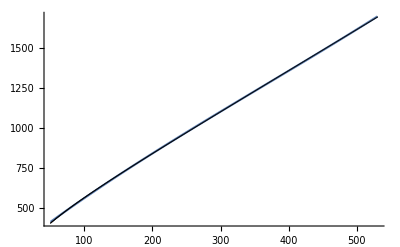

254.32+3.26188 P0-0.00198711 P0^2+1.82689×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em8=fitted
```

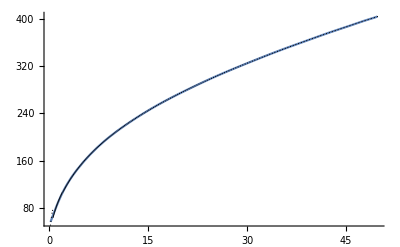

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em8=fitted;
```

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em8=fitted
```

-Graphics-

0.659656+658.782 P0-3385.41 P0^2+8513.26 P0^3-7598.18 P0^4

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em8=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

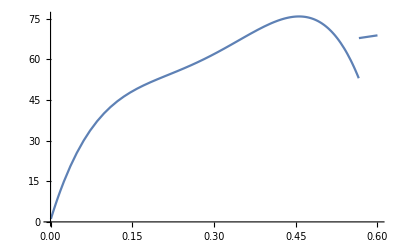

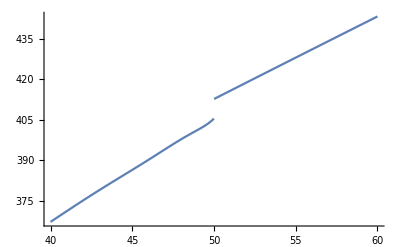

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em8;
FED2[P0_]=fitOuterCoreGUP1Em8;
FED3[P0_]=fitInnerCrustGUP1Em8;
FED4[P0_]=fitOuterCrustGUP1Em8;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em8//FortranForm
```

254.31973251671707 + 3.261877526932941*P0 - 0.001987113156914036*P0**2 + 1.8268897540295154e-6*P0**3

```mathematica
fitOuterCoreGUP1Em8//FortranForm
```

50.988731956384235 + 28.78265687086006*P0 + 3.522828894114323*P0**2 - 3.9081486989415053*P0**3 + 1.2919277799792201*P0**4 - 
     -  0.24898629632433356*P0**5 + 0.03176797506534037*P0**6 - 0.0028394364130570372*P0**7 + 0.00018344054597179885*P0**8 - 
     -  8.71513642334962e-6*P0**9 + 3.0660028823407204e-7*P0**10 - 7.966067022490301e-9*P0**11 + 1.5080426947997883e-10*P0**12 - 
     -  2.0213252641951495e-12*P0**13 + 1.8169434506799985e-14*P0**14 - 9.821725463730458e-17*P0**15 + 2.4128466579501887e-19*P0**16

```mathematica
fitInnerCrustGUP1Em8//FortranForm
```

0.6596556980482654 + 658.7820465828245*P0 - 3385.412057495701*P0**2 + 8513.26060947245*P0**3 - 7598.179318111917*P0**4

```mathematica
fitOuterCrustGUP1Em8//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 1.299108445236239e14*P0**4 + 
     -  2.097713931761943e17*P0**5 - 1.297185952864878e20*P0**6

### fitting energy density GUP 1Em9

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em9 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-9.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={(*dataOuterCore[[1]],dataOuterCore[[2]]*)};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

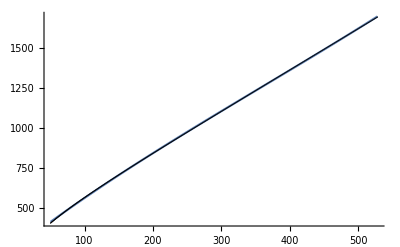

254.547+3.27123 P0-0.00198993 P0^2+1.84224×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em9=fitted
```

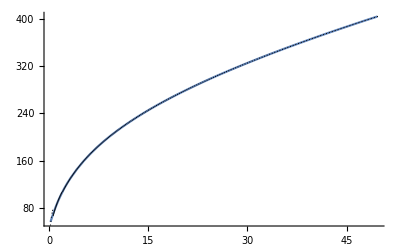

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em9=fitted;
```

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em9=fitted
```

-Graphics-

0.659656+658.782 P0-3385.41 P0^2+8513.26 P0^3-7598.18 P0^4

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em9=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

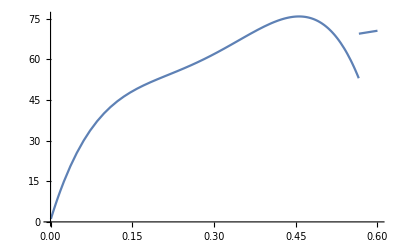

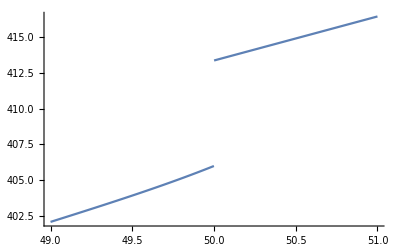

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em9;
FED2[P0_]=fitOuterCoreGUP1Em9;
FED3[P0_]=fitInnerCrustGUP1Em9;
FED4[P0_]=fitOuterCrustGUP1Em9;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,49,51},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em9//FortranForm
```

254.5472555851451 + 3.2712269037830373*P0 - 0.001989925377727716*P0**2 + 1.842240175748262e-6*P0**3

```mathematica
fitOuterCoreGUP1Em9//FortranForm
```

49.36451605135995 + 38.67136097896892*P0 - 5.971069558588728*P0**2 + 0.5280838892749922*P0**3 + 0.07213453678089991*P0**4 - 
     -  0.031943274585310134*P0**5 + 0.005286912083808431*P0**6 - 0.0005395931912018858*P0**7 + 0.00003781696563768739*P0**8 - 
     -  1.8989989196820048e-6*P0**9 + 6.955646370720643e-8*P0**10 - 1.8637558378162894e-9*P0**11 + 3.615446496719337e-11*P0**12 - 
     -  4.943504224112297e-13*P0**13 + 4.5182176197666075e-15*P0**14 - 2.4772670118351236e-17*P0**15 + 6.161038224459982e-20*P0**16

```mathematica
fitInnerCrustGUP1Em9//FortranForm
```

0.6596556980482654 + 658.7820465828245*P0 - 3385.412057495701*P0**2 + 8513.26060947245*P0**3 - 7598.179318111917*P0**4

```mathematica
fitOuterCrustGUP1Em9//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 1.299108445236239e14*P0**4 + 
     -  2.097713931761943e17*P0**5 - 1.297185952864878e20*P0**6